# Lab 5: Splines and 3D Parametric Curves

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,Graphics3D,ListPointPlot3D,RevolutionPlot3D},ImageSize->Small,BaseStyle->{16,FontFamily->"Times"}];
```

```mathematica
(* PROBLEM 1 *)
```

```mathematica
a=4/25
```

4/25

```mathematica
f=a#^2&
```

a #1^2&

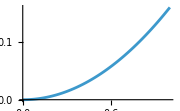

```mathematica
f11=Plot[f[x],{x,0,1}]
```

```mathematica
f14=RevolutionPlot3D[f[x],{x,0,5}]
```

-Graphics3D-

```mathematica
R=10
```

10

```mathematica
f12=ParametricPlot3D[{t*Sin[R*t],t*Cos[R*t],t},{t,0,5}]
```

-Graphics3D-

```mathematica
f13=Graphics3D[{Red,Thickness[0.02],Line[{{7,0,0},{-7/2,7Sqrt[3]/2,0},{7/2,-7Sqrt[3]/2,0},{7,0,0}}]}]
```

-Graphics3D-

```mathematica
{f11,Show[{f12,f13,f14},PlotRange->7]}
```

{-Graphics-,-Graphics3D-}

```mathematica
(* PROBLEM 2 *)
```

```mathematica
G1=ParametricPlot3D[{u,v,0.5},{u,-3,3},{v,-3,3}]
```

-Graphics3D-

```mathematica
cir[R_]:=Graphics3D[{Red,Sphere[{0,0,0.5+R},R]}]
```

```mathematica
All1[R_]:=Show[{G1,cir[R]},PlotRange->{{-4,4},{-4,4},{0,8}}]
```

```mathematica
Manipulate[All1[R],{R,1,3,0.25}]
```

```mathematica
(* Problem 3 *)
```

```mathematica
p33[a_,C_]:=ParametricPlot3D[{Sin[2t],0,Cos[3t]},{t,0,a},PlotStyle->Thickness[C],PlotRange->1]
```

```mathematica
TList={0.01,0.02,0.03,0.04}
```

{0.01,0.02,0.03,0.04}

```mathematica
Manipulate[p33[a,C],{a,0.1,2Pi,0.1},{C,TList}]
```

```mathematica
(* Problem 1 *)
```

```mathematica
data11={{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}
```

{{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}

```mathematica
f11:=Interpolation[data11,Method->"Spline"]
```

```mathematica
f111=Interpolation[data11,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
minx=Min[Transpose[data11][[1]]]
```

-2

```mathematica
maxx=Max[Transpose[data11][[1]]]
```

7

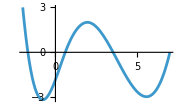

```mathematica
plot11G=Plot[f11[x],{x,minx,maxx}]
```

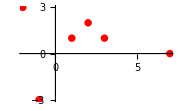

```mathematica
plot11P=ListPlot[data11,PlotStyle->{PointSize[0.03],Red}]
```

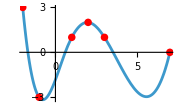

```mathematica
Show[plot11G,plot11P]
```

```mathematica
(* Problem 2 *)
```

```mathematica
x12=Transpose[data11][[1]]
```

{1,-2,-1,7,3,2}

```mathematica
y12=Transpose[data11][[2]]
```

{1,3,-3,0,1,2}

```mathematica
sx12:=Interpolation[x12,Method->"Spline"]
```

```mathematica
sy12:=Interpolation[y12,Method->"Spline"]
```

```mathematica
spline12[t_]:={sx12[t],sy12[t]}
```

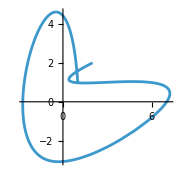

```mathematica
plot12=ParametricPlot[spline12[t],{t,1,Length[x12]}]
```

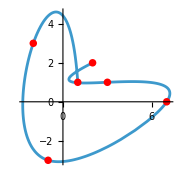

```mathematica
Show[plot12,plot11P]
```

```mathematica
(* Problem 3 *)
```

```mathematica
data3={{-3,-1},{-1,-2},{1,-2},{2,-3},{1,-4},{-1,-4},{-2,-5},{-2,-6},{-1,-6},{-1,-5},{2,-5},{3,-4},{6,-5},{7,-7},{6,-8},{6,-9},{7,-9},{7,-8},{8,-7},{7,-4},{6,-4},{6,-2},{5,0},{10,-1},{7,0},{10,0},{7,1},{10,2},{8,2},{10,3},{6,2},{5,0},{3,0},{1,2},{1,3},{-2,6},{-3,6},{-4,7},{-4,6},{-6,4},{-6,3},{-5,3},{-3,4},{-2,2},{-3,1},{-5,2},{-7,0},{-7,-1},{-6,-1},{-6,0},{-5,1},{-4,0},{-5,-2},{-3,-4},{-2,-4},{-2,-3},{-3,-3},{-4,-2},{-3,-1}};
```

```mathematica
x31=Transpose[data3][[1]]
```

{-3,-1,1,2,1,-1,-2,-2,-1,-1,2,3,6,7,6,6,7,7,8,7,6,6,5,10,7,10,7,10,8,10,6,5,3,1,1,-2,-3,-4,-4,-6,-6,-5,-3,-2,-3,-5,-7,-7,-6,-6,-5,-4,-5,-3,-2,-2,-3,-4,-3}

```mathematica
y31=Transpose[data3][[2]]
```

{-1,-2,-2,-3,-4,-4,-5,-6,-6,-5,-5,-4,-5,-7,-8,-9,-9,-8,-7,-4,-4,-2,0,-1,0,0,1,2,2,3,2,0,0,2,3,6,6,7,6,4,3,3,4,2,1,2,0,-1,-1,0,1,0,-2,-4,-4,-3,-3,-2,-1}

```mathematica
sx31:=Interpolation[x31,Method->"Spline"]
```

```mathematica
sy31:=Interpolation[y31,Method->"Spline"]
```

```mathematica
spline31[t_]:={sx31[t],sy31[t]}
```

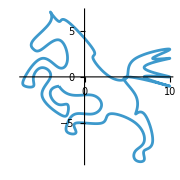

```mathematica
plot31=ParametricPlot[spline31[t],{t,1,Length[x31]}]
```

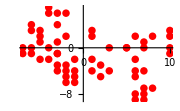

```mathematica
plot32=ListPlot[data3,PlotStyle->{PointSize[0.03],Red}]
```

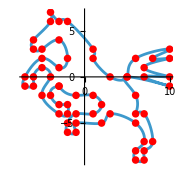

```mathematica
Show[{plot31,plot32}]
```

```mathematica
Plane3=ParametricPlot3D[{x,5,z},{x,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
s3D[t_]:={sx31[t],5,sy31[t]}
```

```mathematica
Horse3=ParametricPlot3D[s3D[t],{t,1,Length[x31]},PlotStyle->Red]
```

-Graphics3D-

```mathematica
VerticalHorse=Show[Horse3,Plane3]
```

-Graphics3D-

```mathematica
(* Problem 4 *)
```

```mathematica
data14={{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}
```

{{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}

```mathematica
x14=Transpose[data14][[1]]
```

{1,2,1,4,4,5,7,5}

```mathematica
y14=Transpose[data14][[2]]
```

{1,3,3,3,4,3,5,5}

```mathematica
z14=Transpose[data14][[3]]
```

{1,1,2,3,4,2,6,5}

```mathematica
sx14=Interpolation[x14]
```

InterpolatingFunction[…]

```mathematica
sy14=Interpolation[y14]
```

InterpolatingFunction[…]

```mathematica
sz14=Interpolation[z14]
```

InterpolatingFunction[…]

```mathematica
s14[t_]:={sx14[t],sy14[t],sz14[t]}
```

```mathematica
k14=ParametricPlot3D[s14[t],{t,1,Length[x14]},PlotStyle->Red]
```

-Graphics3D-

```mathematica
plot14P=ListPointPlot3D[data14,PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
Show[k14,plot14P]
```

-Graphics3D-

```mathematica
(* Problem 5 *)
```

```mathematica
plot5:=ParametricPlot3D[s14[t],{t,1,Length[x14]},PlotStyle->{clr5,Thickness[th5]}]
```

```mathematica
plot5P=ListPointPlot3D[data14,PlotStyle->{PointSize[0.05],Red}]
```

-Graphics3D-

```mathematica
plot5All:=Show[{plot5,plot5P},ImageSize->Small]
```

```mathematica
MyMenu5=PopupMenu[Dynamic[clr5],{Red->"Red",Green->"Green",Blue->"Blue",Purple->"Purple"}]
```

```mathematica
MySlider5={Slider[Dynamic[th5],{0,0.025}],Dynamic[th5]}
```

{,}

```mathematica
{Dynamic[plot5All],MyMenu5,MySlider5}
```

{,,{,}}

```mathematica
(* Bonus *)
```

```mathematica
R=2.5
```

2.5

```mathematica
xx[t_]:=R*Cos[t]
```

```mathematica
yy[t_]:=R*Sin[t]
```

```mathematica
GLine1[t_]:=Graphics3D[{Red,{Arrowheads[0.1],Arrow[{{0,0,0},{xx[t],yy[t],0}}]}}]
```

```mathematica
GLine2[t_]:=Graphics3D[{Blue,{Arrowheads[0.1],Arrow[{{0,0,0},{xx[t+Pi],yy[t+Pi],0}}]}}]
```

```mathematica
Cirt=ParametricPlot3D[{xx[t],yy[t],0},{t,0,2Pi},PlotStyle->Dashed]
```

-Graphics3D-

```mathematica
Manipulate[Show[{GLine1[t],GLine2[t],Cirt}],{t,0,2Pi,Pi/24}]
```

```mathematica
Graphics3D[{Arrowheads[0.1],Arrow[{{0,0,0},{1,1,0}}]}];
```

```mathematica
(* Bonus 1 *)
```

```mathematica
x1[t_,x_,R_]:=t*Sin[R*t]+x
y1[t_,y_,R_]:=t*Cos[R*t]+y
z1[t_]:=t^2/10
```

```mathematica
F1[x_,y_,t_,R_]:={x1[t,x,R],y1[t,y,R],z1[t]}
```

```mathematica
S2={Slider2D[Dynamic[z],{{-15,-15},{15,15}},Background->Yellow,ImageSize->Large],Dynamic[z]}
```

{,}

```mathematica
SR={VerticalSlider[Dynamic[R],{1,5},Background->Yellow],Dynamic[R]}
```

{,}

```mathematica
z={0,0};R=1;
```

```mathematica
Clear[CenterS]
```

```mathematica
CenterS[z_]:=Graphics3D[{Red,PointSize[0.025],Point[{z[[1]],z[[2]],0}]}]
```

```mathematica
Clear[fb]
```

```mathematica
fb[z_,R_]:=ParametricPlot3D[F1[z[[1]],z[[2]],t,R],{t,1,15},PlotRange->{{-20,20},{-20,20},{0,30}},PlotStyle->Black]
```

```mathematica
{Dynamic[Show[fb[z,R],CenterS[z]]],S2,SR}
```

{,{,},{,}}